Problem 4.

```mathematica
WhittakerM 
WhittakerM[k,m,z]gives the Whittaker function Subscript[M, k,m](z)
```

```mathematica
Plot Subscript[M, 2,1/2](x):
```

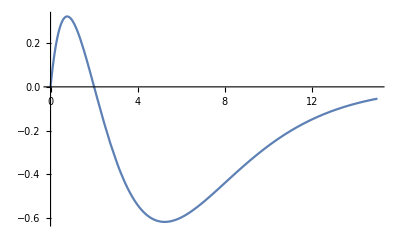

```mathematica
Plot[WhittakerM[2,1/2,x],{x,0,15}]
```

Explanation:
WhittakerM is a mathematical function, suitable for both symbolic and numerical manipulation.
It is related to the hypergeometric function by M_(k,m)(z)==e^(-z/2)z^(m+1/2) _1 F_1(m-k+1/2;1+2m;z). 
M_(k,m)(z) vanishes at z==0 for m>0. 
For certain special arguments, WhittakerM automatically evaluates to exact values.
WhittakerM can be evaluated to arbitrary numerical precision.
WhittakerM automatically threads over lists.
WhittakerM[k,m,z] has a branch cut discontinuity in the complex z plane running from -∞ to 0.

```mathematica
FunctionExpand[WhittakerM[k,m,z]]
```

ⅇ^(-z/2) z^(1/2+m) Hypergeometric1F1[1/2-k+m,1+2 m,z]

Gamma[z] is the Euler gamma function Γ(z) 
Mathematical function, suitable for both symbolic and numerical manipulation.
The gamma function satisfies Γ(z)=∫_0^∞ t^(z-1)e^-t dt. 
Gamma can be evaluated to arbitrary numerical precision.

```mathematica
My Code:
```

WhittakerM[n,1/2+l,(2 r)/n]/(√(n^2 Gamma[-l+n] Gamma[1+l+n]))

-Graphics-

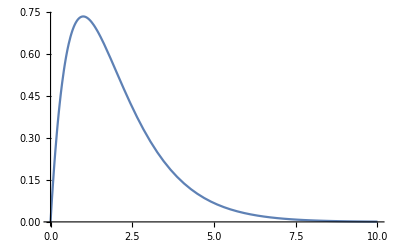

WhittakerM[1,1/2,2 r]

1

```mathematica
Subscript[P,n_,l_][r_]:=1/Sqrt[n^2 Gamma[n+l+1]Gamma[n-l]] WhittakerM[n,l+1/2,2 r/n];
Plot[Subscript[P, 1,0][r], {r,0,10}] Gamma
Subscript[P, 1,0][r]
Integrate[(Subscript[P, 1,0][r])^2, {r, 0, ∞}]
```

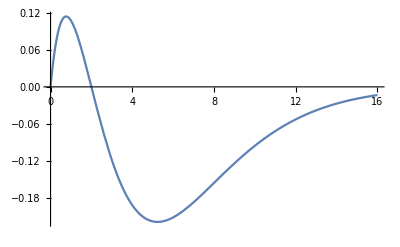

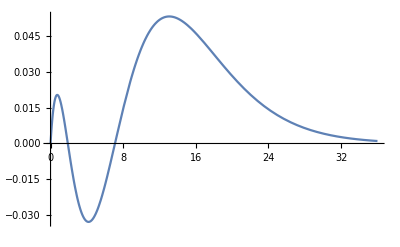

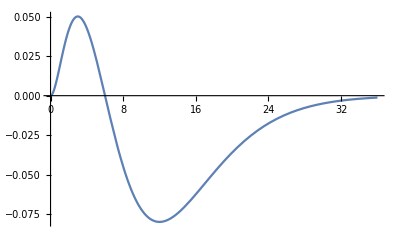

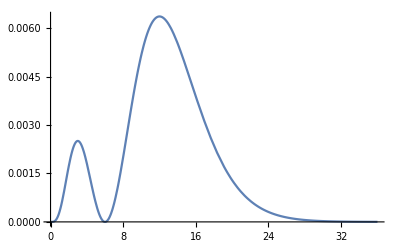

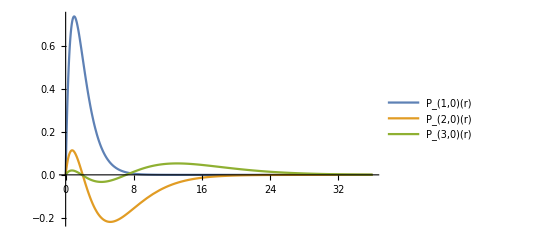

```mathematica
Plot[Subscript[P, 2,0][r], {r,0,16},PlotLegends->"P_(2  s)(r)"] (* 4 n^2 should span almost all of the essential part of the wavefunction *)
Plot[Subscript[P, 3,0][r], {r,0,36},PlotLegends->"P_(3  s)(r)"]
Plot[Subscript[P, 3,1][r], {r,0,36},PlotLegends->"P_(3  p)(r)"]
Plot[(Subscript[P, 3,1][r])^2, {r,0,36},PlotLegends->"P_(3  p)(r)^2"]
Plot[{Subscript[P, 1,0][r],Subscript[P, 2,0][r],Subscript[P, 3,0][r]}, {r,0,36}, PlotRange->All, PlotLegends->"Expressions"]
```

## Problem 5.

```mathematica
Plot Subscript[P, 17p](r) and calculate numerically ∫dr Subscript[P, 17p](r)Subscript[P, 17p](r) and ∫dr r Subscript[P, 17p](r)Subscript[P, 17p](r)
```

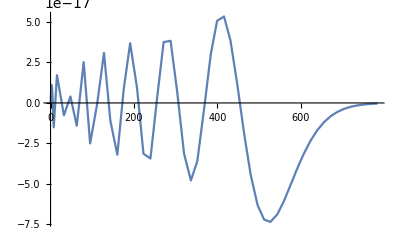

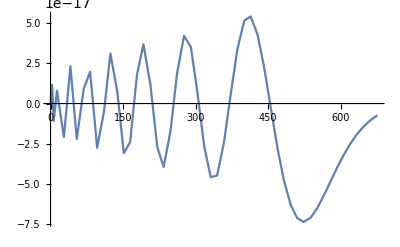

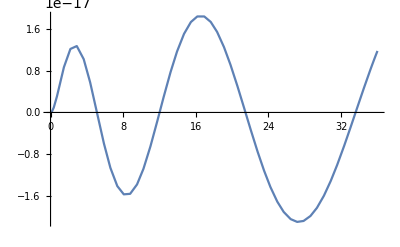

```mathematica
Plot[Subscript[P, 17,1][r], {r,0,4*14^2}]
Plot[Subscript[P, 17,1][r], {r,0,4*13^2}]
Plot[Subscript[P, 17,1][r], {r,0, 36}]
```

```mathematica
NIntegrate[(Subscript[P, 17,1][r])^2, {r, 0, 4*15^2}]
Integrate[(Subscript[P, 17,1][r])^2, {r, 0, ∞}]
```

8.78255×10^-31

1/1138621918549924531666944000000

```mathematica
NIntegrate[r  (Subscript[P, 17,1][r])^2, {r, 0, 4*15^2}]
```

3.79845×10^-28

## Problem 6.

```mathematica
K   4s  IP  = -0.159516450 Ha 

K  10s  -0.151335152 Ha 
Subscript[IP, 10s] ->  (-0.159516450 + 0.151335152) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 7.817608

K  9s  -0.148756833Ha 
Subscript[IP, 9s] ->  (-0.159516450 +0.148756833) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 6.816895

K  8s  -0.144733706Ha 
Subscript[IP, 8s] ->  (-0.159516450 +0.144733706) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 5.815773

K  7s  -0.137939627Ha 
Subscript[IP, 7s] ->  (-0.159516450 +0.137939627) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 4.813836

K  6s  -0.125074640Ha 
Subscript[IP, 6s] ->  (-0.159516450 +0.125074640) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 3.810149

K  5s  -0.095804016Ha 
Subscript[IP, 5s] ->  (-0.159516450 +0.095804016) Ha = -1/(2 n^(*2))Ha
SuperStar[n]= 2.801386
```

## n^*=n-µ

```mathematica
where µ = quantum defect
Subscript[E, nl]=-1/(2(n-Subscript[µ, l])^2)->Subscript[µ, l]=n-√(-1/(2 Subscript[E, nl]))
Subscript[µ, l,10s]=10-7.817608=2.182392, Subscript[IP, 10s]=0.008181298 Ha
Subscript[µ, l,9s]=9-6.816895=2.183105, Subscript[IP, 9s] =0.010759617Ha
Subscript[µ, l,8s]=8-5.815773 =2.184227, Subscript[IP, 8s]=0.014782744Ha
Subscript[µ, l,7s]=7-4.813836=2.186164, Subscript[IP, 7s]=0.021576823Ha
Subscript[µ, l,6s]=6- 3.810149=2.189851, Subscript[IP, 6s]=0.03444181Ha
Subscript[µ, l,5s]=5-2.801386=2.198614,  Subscript[IP, 5s]=0.063712434Ha
```

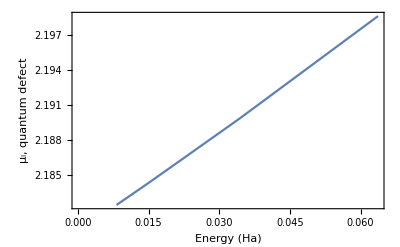

```mathematica
(* Just made a table to make a plot *)
ListLinePlot[{{0.063712434, 2.198614},
{0.03444181,2.189851},
{0.021576823, 2.186164},
{0.014782744, 2.184227},
{0.010759617, 2.183105},
{0.008181298, 2.182392}}, FrameLabel->{"Energy (Ha)", "µ_l, quantum defect"},Frame->True, FrameStyle->Directive[Brown,Thick, 14]]
```